

```mathematica
Plot[x,{x,-2,2}]
```

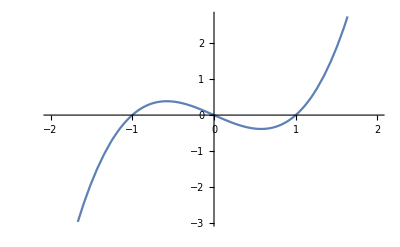

```mathematica
Plot[x^3-x,{x,-2,2}]
```

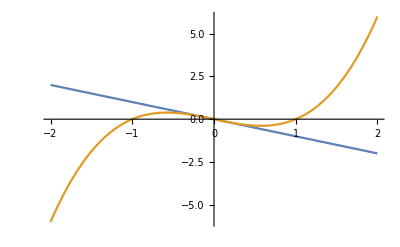

```mathematica
Plot[{-x,x^3-x},{x,-2,2}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,x^3-x}.Normalize@{1,0}],x∈Reals]
```

1/(√(2-2 x^2+x^4))

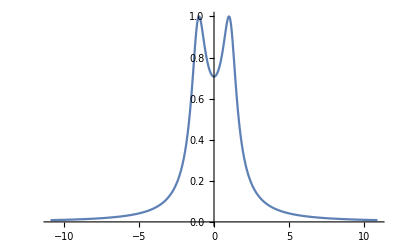

```mathematica
Plot[1/(√(2-2 x^2+x^4)),{x,-10.92,10.92}]
```

```mathematica
D[1/(√(2-2 x^2+x^4)),x]
```

-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2))

```mathematica
Simplify[-(-4 x+4 x^3)/(2 (2-2 x^2+x^4)^(3/2))]
```

-(2 x (-1+x^2))/((2-2 x^2+x^4)^(3/2))

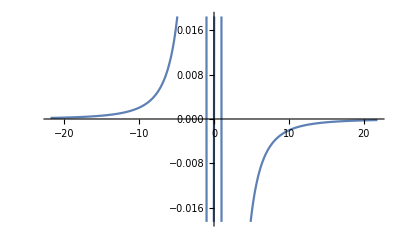

```mathematica
Plot[-(2 x (-1+x^2))/((2-2 x^2+x^4)^(3/2)),{x,-21.84,21.84}]
```

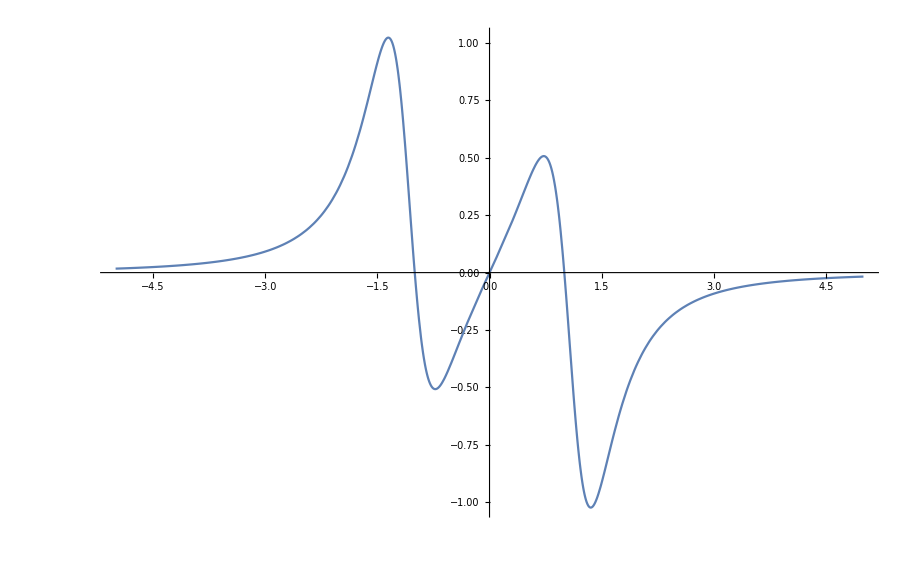

```mathematica
Plot[-(2 x (-1+x^2))/((2-2 x^2+x^4)^(3/2)),{x,-5,5}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,x^3-x}.Normalize@{1,a}],{a,x}∈Reals]
```

Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))

```mathematica
Manipulate[Plot[Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4))),{x,-1.2071233521140896,1.2071233521140896}],{a,-1.5531229146464538,1.5531229146464538}]
```

```mathematica
Manipulate[
Plot[Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))
,{x,-2,2}]
,{a,-5,5}]
```

```mathematica
Manipulate[
Plot[Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))
,{x,-2,2}
,PlotRange->{{-5,5},{-2,2}}]
,{a,-5,5}]
```

```mathematica
Manipulate[
Plot[
{a,Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))}
,{x,-2,2}
,PlotRange->{{-5,5},{-2,2}}]
,{a,-5,5}]
```

```mathematica
Manipulate[
Plot[
{a,Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))}
,{x,-2,2}
,PlotRange->{{-2,2},{-5,5}}]
,{a,-5,5}]
```

```mathematica
Plot3D[
Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))
,{x,-2,2},{a,-5,5}
,PlotRange->{{-2,2},{-5,5}}]
```

-Graphics3D-

```mathematica
Manipulate[
Plot[
{a,Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))}
,{x,-2,2}
,PlotRange->{{-2,2},{-10,10}}]
,{a,-10,10}]
```

```mathematica
Plot3D[
Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))
,{x,-2,2},{a,-5,5}
,PlotRange->Full]
```

-Graphics3D-

```mathematica
Manipulate[
Plot[
{a,Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))}
,{x,-2,2}
,PlotRange->{{-2,2},{-5,5}}]
,{a,-5,5}]
```

```mathematica
ContourPlot3D[Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))==1,{x,-2,2},{a,-5,5}]
```

ContourPlot3D::argrx: ContourPlot3D called with 3 arguments; 4 arguments are expected.

ContourPlot3D[Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))==1,{x,-2,2},{a,-5,5}]

```mathematica
ContourPlot[Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))==1,{x,-2,2},{a,-5,5}]
```

-Graphics-

```mathematica
Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))==1
```

Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))==1

```mathematica
Reduce[Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))==1]
```

$Aborted

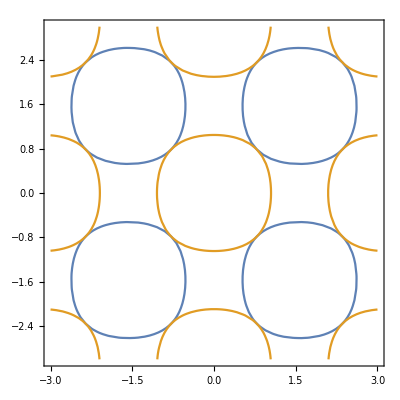

```mathematica
ContourPlot[{Abs[Sin[x]Sin[y]]==0.5,Abs[Cos[x]Cos[y]]==0.5},{x,-3,3},{y,-3,3}]
```

```mathematica
ContourPlot[{Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))==1,Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4)))==0},{x,-2,2},{a,-5,5}]
```

-Graphics-

```mathematica
Plot[{-x,x^3-x},{x,-2,2}]
```

-Graphics-

```mathematica
Abs@{-x,x^3-x}
```

{Abs[x],Abs[-x+x^3]}

```mathematica
FullSimplify[{Abs[x],Abs[-x+x^3]}/(Total@{Abs[x],Abs[-x+x^3]}),x∈Reals]
```

{1/(1+Abs[-1+x^2]),1-1/(1+Abs[-1+x^2])}

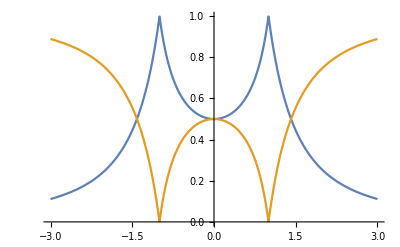

```mathematica
Plot[{1/(1+Abs[-1+x^2]),1-1/(1+Abs[-1+x^2])},{x,-3,3}]
```

```mathematica
Reduce[Total@{1/(1+Abs[-1+x^2]),1-1/(1+Abs[-1+x^2])}==1,x]
```

True

```mathematica
(Abs@{x,x^3})/Total[Abs@{x,x^3}]
```

{Abs[x]/(Abs[x]+Abs[x]^3),Abs[x]^3/(Abs[x]+Abs[x]^3)}

```mathematica
FullSimplify[(Abs@{x,x^3})/Total[Abs@{x,x^3}],x∈Reals]
```

{1/(1+x^2),x^2/(1+x^2)}

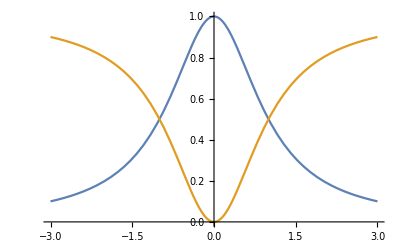

```mathematica
Plot[{1/(1+x^2),x^2/(1+x^2)},{x,-3,3}]
```

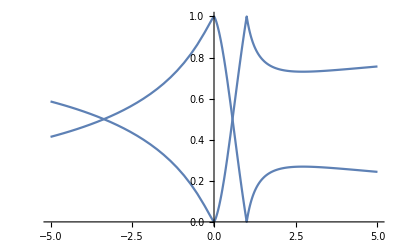

```mathematica
With[{funcs={x,Log[x]}},
Plot[FullSimplify[(Abs@funcs)/Total[Abs@funcs],x∈Reals],{x,-5,5}]
]
```

```mathematica
With[{funcs={x,Log[x]}},
Plot[FullSimplify[(Abs@funcs)/Total[Abs@funcs],x∈Reals],{x,-5,5},PlotLegends->"Expressions"]
]
```

-Graphics-

```mathematica
With[{funcs={x,Log[x]}},
Plot[FullSimplify[D[(Abs@funcs)/Total[Abs@funcs],x],x∈Reals],{x,-5,5},PlotLegends->"Expressions"]
]
```

General::ivar: -4.9998 is not a valid variable.

General::ivar: -4.79571 is not a valid variable.

General::ivar: -4.59163 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
(Abs@D[{x,x^3},x])/Total[Abs@D[{x,x^3},x]]
```

{1/(1+3 Abs[x]^2),(3 Abs[x]^2)/(1+3 Abs[x]^2)}

```mathematica
FullSimplify[(Abs@D[{x,x^3},x])/Total[Abs@D[{x,x^3},x]],x∈Reals]
```

{1/(1+3 x^2),(3 x^2)/(1+3 x^2)}

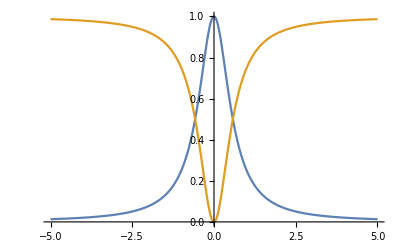

```mathematica
Plot[{1/(1+3 x^2),(3 x^2)/(1+3 x^2)},{x,-5,5}]
```

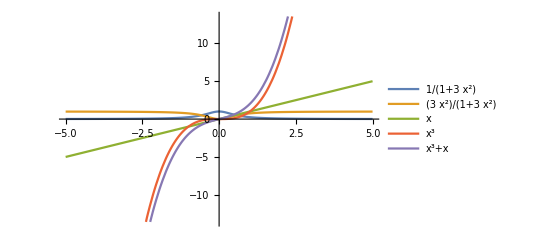

```mathematica
Plot[{1/(1+3 x^2),(3 x^2)/(1+3 x^2),x,x^3,x^3+x},{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
Plot3D[
{Abs[1+a (-1+x^2)]/(√((1+a^2) (2-2 x^2+x^4))),1}
,{x,-2,2},{a,-5,5}
,PlotRange->Full]
```

-Graphics3D-



```mathematica
Plot[x^2,{x,-2,2}]
```

```mathematica
FullSimplify[Normalize@{1,2x}.Normalize@{1,1},x∈Reals]
```

(1+2 x)/(√(2+8 x^2))

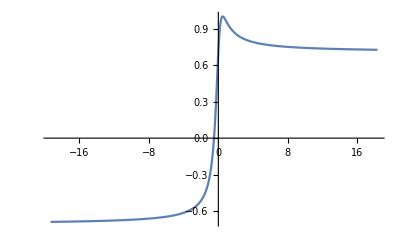

```mathematica
Plot[(1+2 x)/(√(2+8 x^2)),{x,-19.30666666666667,18.30666666666667}]
```

```mathematica
D[(1+2 x)/(√(2+8 x^2)),x]
```

-(8 x (1+2 x))/((2+8 x^2)^(3/2))+2/(√(2+8 x^2))

```mathematica
Simplify[-(8 x (1+2 x))/((2+8 x^2)^(3/2))+2/(√(2+8 x^2))]
```

(√2 (1-2 x))/((1+4 x^2)^(3/2))

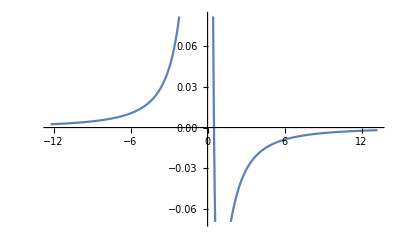

```mathematica
Plot[(√2 (1-2 x))/((1+4 x^2)^(3/2)),{x,-12.239999999999998,13.239999999999998}]
```

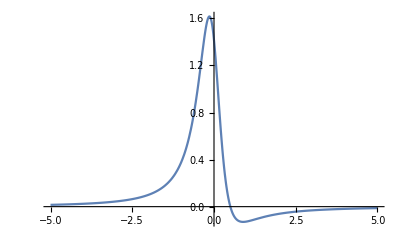

```mathematica
Plot[(√2 (1-2 x))/((1+4 x^2)^(3/2)),{x,-5,5},PlotRange->Full]
```

```mathematica
Manipulate[
NIntegrate[(√2 (1-2 x))/((1+4 x^2)^(3/2)),{x,-a,a}]
,{a,0.01,100}]
```

```mathematica
Limit[∫_-a^a (√2 (1-2 x))/((1+4 x^2)^(3/2))ⅆx,a->∞]
```

√2

```mathematica
FullSimplify[Normalize@{1,1}.Normalize@{1,1},x∈Reals]
```

1

```mathematica
2/((√(1+4 x^2))^3)
```

2/((1+4 x^2)^(3/2))

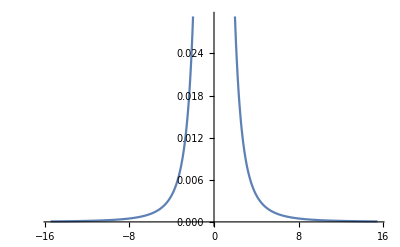

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-15.469999999999999,15.469999999999999}]
```

```mathematica
Limit[∫_-a^a 2/((1+4 x^2)^(3/2))ⅆx,a->∞]
```

2

```mathematica
FullSimplify[Normalize@{1,3 x^2}.Normalize@{1,1},x∈Reals]
```

(1+3 x^2)/(√(2+18 x^4))

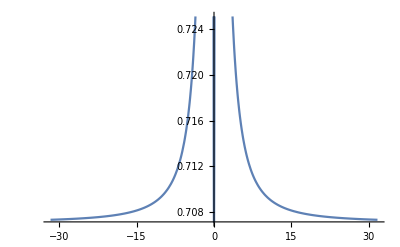

```mathematica
Plot[(1+3 x^2)/(√(2+18 x^4)),{x,-31.72,31.72}]
```

```mathematica
D[(1+3 x^2)/(√(2+18 x^4)), x]
```

-(36 x^3 (1+3 x^2))/((2+18 x^4)^(3/2))+(6 x)/(√(2+18 x^4))

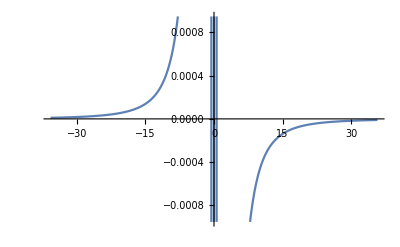

```mathematica
Plot[-(36 x^3 (1+3 x^2))/((2+18 x^4)^(3/2))+(6 x)/(√(2+18 x^4)),{x,-35.79333333333334,35.79333333333334}]
```

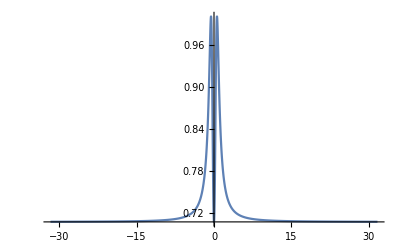

```mathematica
Plot[(1+3 x^2)/(√(2+18 x^4)),{x,-31.72,31.72},PlotRange->Full]
```

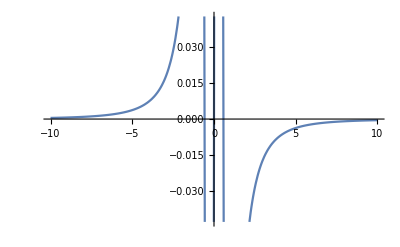

```mathematica
Plot[-(36 x^3 (1+3 x^2))/((2+18 x^4)^(3/2))+(6 x)/(√(2+18 x^4)),{x,-10,10}]
```

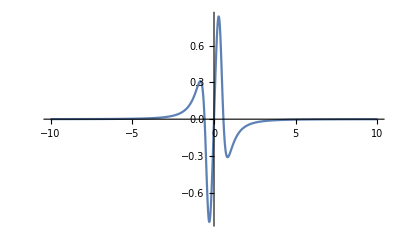

```mathematica
Plot[-(36 x^3 (1+3 x^2))/((2+18 x^4)^(3/2))+(6 x)/(√(2+18 x^4)),{x,-10,10},PlotRange->Full]
```

```mathematica
Limit[∫_-a^a (-(36 x^3 (1+3 x^2))/((2+18 x^4)^(3/2))+(6 x)/(√(2+18 x^4)))ⅆx,a->∞]
```

0

```mathematica
Limit[∫_-a^a Abs[(-(36 x^3 (1+3 x^2))/((2+18 x^4)^(3/2))+(6 x)/(√(2+18 x^4)))]ⅆx,a->∞]
```

-2 √2

```mathematica
y''[x]/((√(1+y'[x]^2))^3)
```

y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
With[{y=Function[x,x^3]},
y''[x]/((√(1+y'[x]^2))^3)
]
```

(6 x)/((1+9 x^4)^(3/2))

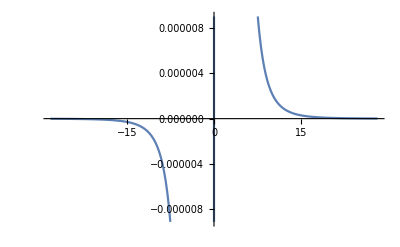

```mathematica
Plot[(6 x)/((1+9 x^4)^(3/2)),{x,-28.21,28.21}]
```

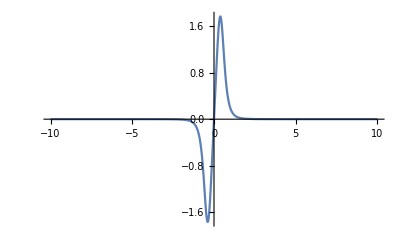

```mathematica
Plot[(6 x)/((1+9 x^4)^(3/2)),{x,-10,10},PlotRange->Full]
```

```mathematica
Limit[∫_-a^a Abs[(6 x)/((1+9 x^4)^(3/2))]ⅆx,a->∞]
```

2

```mathematica
Limit[∫_0^a Abs[(6 x)/((1+9 x^4)^(3/2))]ⅆx,a->∞]
```

$Aborted

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Normal[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

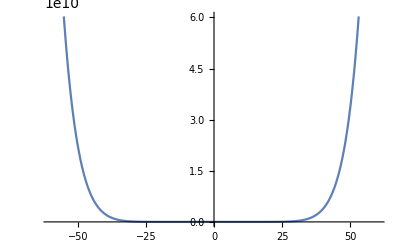

```mathematica
Plot[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800,{x,-60.,60.}]
```

```mathematica
Manipulate[
Plot[{Exp[x],Normal[Series[Exp[x],{x,0,a}]]},{x,-10,10}]
,{a,0,10}]
```

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
Manipulate[
Plot[{Exp[x],Normal[Series[Exp[x],{x,0,a}]]},{x,-10,10}]
,{a,1,10,1}]
```

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

```mathematica
Manipulate[
With[{approx=Normal[Series[Exp[x],{x,0,a}]]},
Plot[{Exp[x],approx},{x,-10,10}]
]
,{a,1,10,1}]
```

```mathematica
∑_(i=0)^n π
```

(1+n) π

```mathematica
∑_(i=1)^n π+1/n(-1)^i
```

(-1)^i/n+n π

```mathematica
∑_(i=1)^n (π+1/n(-1)^i)
```

(-1+(-1)^n+2 n^2 π)/(2 n)

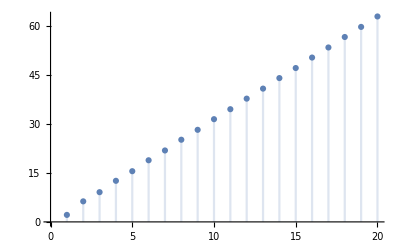

```mathematica
DiscretePlot[(-1+(-1)^n+2 n^2 π)/(2 n),{n,1,20}]
```

```mathematica
∑_(i=1)^n (π+1/i(-1)^i)
```

n π+(-1)^n LerchPhi[-1,1,1+n]-Log[2]

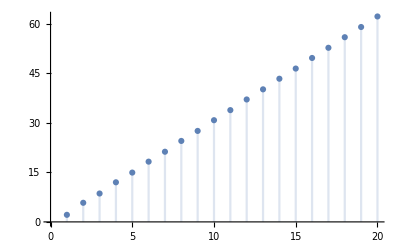

```mathematica
DiscretePlot[n π+(-1)^n LerchPhi[-1,1,1+n]-Log[2],{n,1,20}]
```

```mathematica
∑_(i=1)^n (1/i(-1)^i)
```

(-1)^n LerchPhi[-1,1,1+n]-Log[2]

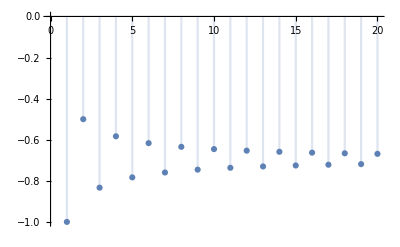

```mathematica
DiscretePlot[(-1)^n LerchPhi[-1,1,1+n]-Log[2],{n,1,20}]
```

```mathematica
∑_(i=1)^n (1/(2i)(-1)^i)
```

1/2 ((-1)^n LerchPhi[-1,1,1+n]-Log[2])

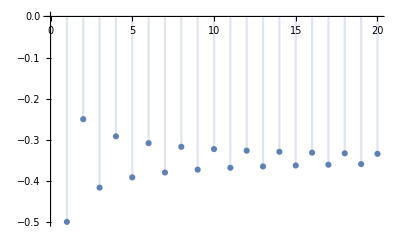

```mathematica
DiscretePlot[1/2 ((-1)^n LerchPhi[-1,1,1+n]-Log[2]),{n,1,20}]
```

```mathematica
Limit[∑_(i=1)^n (1/(2i)(-1)^i),n->∞]
```

-Log[2]/2

```mathematica
N[-Log[2]/2]
```

-0.346574

```mathematica
∑_(i=1)^n (1/(2i)(-1)^i)-Log[2]/2
```

1/2 ((-1)^n LerchPhi[-1,1,1+n]-Log[2])-Log[2]/2

```mathematica
∑_(i=1)^n (1/(2i)(-1)^i)+Log[2]/2
```

1/2 ((-1)^n LerchPhi[-1,1,1+n]-Log[2])+Log[2]/2

```mathematica
Simplify[1/2 ((-1)^n LerchPhi[-1,1,1+n]-Log[2])+Log[2]/2]
```

1/2 (-1)^n LerchPhi[-1,1,1+n]

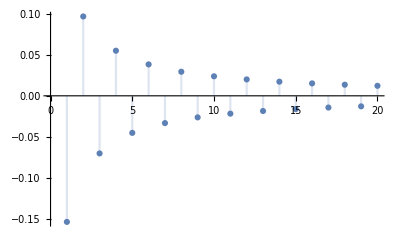

```mathematica
DiscretePlot[1/2 (-1)^n LerchPhi[-1,1,1+n],{n,1,20}]
```

```mathematica
LerchPhi
```

LerchPhi

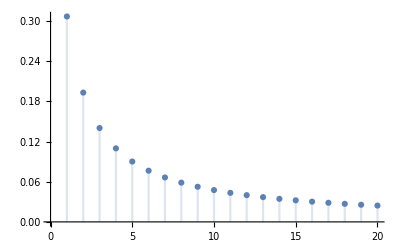

```mathematica
DiscretePlot[LerchPhi[-1,1,1+n],{n,1,20}]
```

```mathematica
Series[x^2,{x,0,10}]
```

x^2+O[x]^11

```mathematica
Series[Gamma[x],{x,0,10}]
```

1/x-EulerGamma+1/12 (6 EulerGamma^2+π^2) x+1/6 (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1]) x^2+1/24 (EulerGamma^4+EulerGamma^2 π^2+(3 π^4)/20-4 EulerGamma PolyGamma[2,1]) x^3+1/120 (-EulerGamma^5-(5 EulerGamma^3 π^2)/3-(3 EulerGamma π^4)/4+10 EulerGamma^2 PolyGamma[2,1]+5/3 π^2 PolyGamma[2,1]+PolyGamma[4,1]) x^4+1/720 (EulerGamma^6+(5 EulerGamma^4 π^2)/2+(9 EulerGamma^2 π^4)/4+(61 π^6)/168-20 EulerGamma^3 PolyGamma[2,1]-10 EulerGamma π^2 PolyGamma[2,1]+10 PolyGamma[2,1]^2-6 EulerGamma PolyGamma[4,1]) x^5+1/5040(-EulerGamma^7-(7 EulerGamma^5 π^2)/2-(21 EulerGamma^3 π^4)/4-(61 EulerGamma π^6)/24+35 EulerGamma^4 PolyGamma[2,1]+35 EulerGamma^2 π^2 PolyGamma[2,1]+21/4 π^4 PolyGamma[2,1]-70 EulerGamma PolyGamma[2,1]^2+21 EulerGamma^2 PolyGamma[4,1]+7/2 π^2 PolyGamma[4,1]+PolyGamma[6,1]) x^6+1/40320(EulerGamma^8+(14 EulerGamma^6 π^2)/3+(21 EulerGamma^4 π^4)/2+(61 EulerGamma^2 π^6)/6+(1261 π^8)/720-56 EulerGamma^5 PolyGamma[2,1]-280/3 EulerGamma^3 π^2 PolyGamma[2,1]-42 EulerGamma π^4 PolyGamma[2,1]+280 EulerGamma^2 PolyGamma[2,1]^2+140/3 π^2 PolyGamma[2,1]^2-56 EulerGamma^3 PolyGamma[4,1]-28 EulerGamma π^2 PolyGamma[4,1]+56 PolyGamma[2,1] PolyGamma[4,1]-8 EulerGamma PolyGamma[6,1]) x^7+1/362880(-EulerGamma^9-6 EulerGamma^7 π^2-(189 EulerGamma^5 π^4)/10-(61 EulerGamma^3 π^6)/2-(1261 EulerGamma π^8)/80+84 EulerGamma^6 PolyGamma[2,1]+210 EulerGamma^4 π^2 PolyGamma[2,1]+189 EulerGamma^2 π^4 PolyGamma[2,1]+61/2 π^6 PolyGamma[2,1]-840 EulerGamma^3 PolyGamma[2,1]^2-420 EulerGamma π^2 PolyGamma[2,1]^2+280 PolyGamma[2,1]^3+126 EulerGamma^4 PolyGamma[4,1]+126 EulerGamma^2 π^2 PolyGamma[4,1]+189/10 π^4 PolyGamma[4,1]-504 EulerGamma PolyGamma[2,1] PolyGamma[4,1]+36 EulerGamma^2 PolyGamma[6,1]+6 π^2 PolyGamma[6,1]+PolyGamma[8,1]) x^8+1/3628800(EulerGamma^10+(15 EulerGamma^8 π^2)/2+(63 EulerGamma^6 π^4)/2+(305 EulerGamma^4 π^6)/4+(1261 EulerGamma^2 π^8)/16+(4977 π^10)/352-120 EulerGamma^7 PolyGamma[2,1]-420 EulerGamma^5 π^2 PolyGamma[2,1]-630 EulerGamma^3 π^4 PolyGamma[2,1]-305 EulerGamma π^6 PolyGamma[2,1]+2100 EulerGamma^4 PolyGamma[2,1]^2+2100 EulerGamma^2 π^2 PolyGamma[2,1]^2+315 π^4 PolyGamma[2,1]^2-2800 EulerGamma PolyGamma[2,1]^3-252 EulerGamma^5 PolyGamma[4,1]-420 EulerGamma^3 π^2 PolyGamma[4,1]-189 EulerGamma π^4 PolyGamma[4,1]+2520 EulerGamma^2 PolyGamma[2,1] PolyGamma[4,1]+420 π^2 PolyGamma[2,1] PolyGamma[4,1]+126 PolyGamma[4,1]^2-120 EulerGamma^3 PolyGamma[6,1]-60 EulerGamma π^2 PolyGamma[6,1]+120 PolyGamma[2,1] PolyGamma[6,1]-10 EulerGamma PolyGamma[8,1]) x^9+1/39916800(-EulerGamma^11-(55 EulerGamma^9 π^2)/6-(99 EulerGamma^7 π^4)/2-(671 EulerGamma^5 π^6)/4-(13871 EulerGamma^3 π^8)/48-(4977 EulerGamma π^10)/32+165 EulerGamma^8 PolyGamma[2,1]+770 EulerGamma^6 π^2 PolyGamma[2,1]+3465/2 EulerGamma^4 π^4 PolyGamma[2,1]+3355/2 EulerGamma^2 π^6 PolyGamma[2,1]+13871/48 π^8 PolyGamma[2,1]-4620 EulerGamma^5 PolyGamma[2,1]^2-7700 EulerGamma^3 π^2 PolyGamma[2,1]^2-3465 EulerGamma π^4 PolyGamma[2,1]^2+15400 EulerGamma^2 PolyGamma[2,1]^3+7700/3 π^2 PolyGamma[2,1]^3+462 EulerGamma^6 PolyGamma[4,1]+1155 EulerGamma^4 π^2 PolyGamma[4,1]+2079/2 EulerGamma^2 π^4 PolyGamma[4,1]+671/4 π^6 PolyGamma[4,1]-9240 EulerGamma^3 PolyGamma[2,1] PolyGamma[4,1]-4620 EulerGamma π^2 PolyGamma[2,1] PolyGamma[4,1]+4620 PolyGamma[2,1]^2 PolyGamma[4,1]-1386 EulerGamma PolyGamma[4,1]^2+330 EulerGamma^4 PolyGamma[6,1]+330 EulerGamma^2 π^2 PolyGamma[6,1]+99/2 π^4 PolyGamma[6,1]-1320 EulerGamma PolyGamma[2,1] PolyGamma[6,1]+55 EulerGamma^2 PolyGamma[8,1]+55/6 π^2 PolyGamma[8,1]+PolyGamma[10,1]) x^10+O[x]^11

```mathematica
Normal[%95]
```

-EulerGamma+1/x+1/12 (6 EulerGamma^2+π^2) x+1/6 x^2 (-EulerGamma^3-(EulerGamma π^2)/2+PolyGamma[2,1])+1/24 x^3 (EulerGamma^4+EulerGamma^2 π^2+(3 π^4)/20-4 EulerGamma PolyGamma[2,1])+1/120 x^4 (-EulerGamma^5-(5 EulerGamma^3 π^2)/3-(3 EulerGamma π^4)/4+10 EulerGamma^2 PolyGamma[2,1]+5/3 π^2 PolyGamma[2,1]+PolyGamma[4,1])+1/720 x^5 (EulerGamma^6+(5 EulerGamma^4 π^2)/2+(9 EulerGamma^2 π^4)/4+(61 π^6)/168-20 EulerGamma^3 PolyGamma[2,1]-10 EulerGamma π^2 PolyGamma[2,1]+10 PolyGamma[2,1]^2-6 EulerGamma PolyGamma[4,1])+1/5040 x^6 (-EulerGamma^7-(7 EulerGamma^5 π^2)/2-(21 EulerGamma^3 π^4)/4-(61 EulerGamma π^6)/24+35 EulerGamma^4 PolyGamma[2,1]+35 EulerGamma^2 π^2 PolyGamma[2,1]+21/4 π^4 PolyGamma[2,1]-70 EulerGamma PolyGamma[2,1]^2+21 EulerGamma^2 PolyGamma[4,1]+7/2 π^2 PolyGamma[4,1]+PolyGamma[6,1])+1/40320 x^7 (EulerGamma^8+(14 EulerGamma^6 π^2)/3+(21 EulerGamma^4 π^4)/2+(61 EulerGamma^2 π^6)/6+(1261 π^8)/720-56 EulerGamma^5 PolyGamma[2,1]-280/3 EulerGamma^3 π^2 PolyGamma[2,1]-42 EulerGamma π^4 PolyGamma[2,1]+280 EulerGamma^2 PolyGamma[2,1]^2+140/3 π^2 PolyGamma[2,1]^2-56 EulerGamma^3 PolyGamma[4,1]-28 EulerGamma π^2 PolyGamma[4,1]+56 PolyGamma[2,1] PolyGamma[4,1]-8 EulerGamma PolyGamma[6,1])+1/362880 x^8 (-EulerGamma^9-6 EulerGamma^7 π^2-(189 EulerGamma^5 π^4)/10-(61 EulerGamma^3 π^6)/2-(1261 EulerGamma π^8)/80+84 EulerGamma^6 PolyGamma[2,1]+210 EulerGamma^4 π^2 PolyGamma[2,1]+189 EulerGamma^2 π^4 PolyGamma[2,1]+61/2 π^6 PolyGamma[2,1]-840 EulerGamma^3 PolyGamma[2,1]^2-420 EulerGamma π^2 PolyGamma[2,1]^2+280 PolyGamma[2,1]^3+126 EulerGamma^4 PolyGamma[4,1]+126 EulerGamma^2 π^2 PolyGamma[4,1]+189/10 π^4 PolyGamma[4,1]-504 EulerGamma PolyGamma[2,1] PolyGamma[4,1]+36 EulerGamma^2 PolyGamma[6,1]+6 π^2 PolyGamma[6,1]+PolyGamma[8,1])+1/3628800 x^9 (EulerGamma^10+(15 EulerGamma^8 π^2)/2+(63 EulerGamma^6 π^4)/2+(305 EulerGamma^4 π^6)/4+(1261 EulerGamma^2 π^8)/16+(4977 π^10)/352-120 EulerGamma^7 PolyGamma[2,1]-420 EulerGamma^5 π^2 PolyGamma[2,1]-630 EulerGamma^3 π^4 PolyGamma[2,1]-305 EulerGamma π^6 PolyGamma[2,1]+2100 EulerGamma^4 PolyGamma[2,1]^2+2100 EulerGamma^2 π^2 PolyGamma[2,1]^2+315 π^4 PolyGamma[2,1]^2-2800 EulerGamma PolyGamma[2,1]^3-252 EulerGamma^5 PolyGamma[4,1]-420 EulerGamma^3 π^2 PolyGamma[4,1]-189 EulerGamma π^4 PolyGamma[4,1]+2520 EulerGamma^2 PolyGamma[2,1] PolyGamma[4,1]+420 π^2 PolyGamma[2,1] PolyGamma[4,1]+126 PolyGamma[4,1]^2-120 EulerGamma^3 PolyGamma[6,1]-60 EulerGamma π^2 PolyGamma[6,1]+120 PolyGamma[2,1] PolyGamma[6,1]-10 EulerGamma PolyGamma[8,1])+1/39916800 x^10 (-EulerGamma^11-(55 EulerGamma^9 π^2)/6-(99 EulerGamma^7 π^4)/2-(671 EulerGamma^5 π^6)/4-(13871 EulerGamma^3 π^8)/48-(4977 EulerGamma π^10)/32+165 EulerGamma^8 PolyGamma[2,1]+770 EulerGamma^6 π^2 PolyGamma[2,1]+3465/2 EulerGamma^4 π^4 PolyGamma[2,1]+3355/2 EulerGamma^2 π^6 PolyGamma[2,1]+13871/48 π^8 PolyGamma[2,1]-4620 EulerGamma^5 PolyGamma[2,1]^2-7700 EulerGamma^3 π^2 PolyGamma[2,1]^2-3465 EulerGamma π^4 PolyGamma[2,1]^2+15400 EulerGamma^2 PolyGamma[2,1]^3+7700/3 π^2 PolyGamma[2,1]^3+462 EulerGamma^6 PolyGamma[4,1]+1155 EulerGamma^4 π^2 PolyGamma[4,1]+2079/2 EulerGamma^2 π^4 PolyGamma[4,1]+671/4 π^6 PolyGamma[4,1]-9240 EulerGamma^3 PolyGamma[2,1] PolyGamma[4,1]-4620 EulerGamma π^2 PolyGamma[2,1] PolyGamma[4,1]+4620 PolyGamma[2,1]^2 PolyGamma[4,1]-1386 EulerGamma PolyGamma[4,1]^2+330 EulerGamma^4 PolyGamma[6,1]+330 EulerGamma^2 π^2 PolyGamma[6,1]+99/2 π^4 PolyGamma[6,1]-1320 EulerGamma PolyGamma[2,1] PolyGamma[6,1]+55 EulerGamma^2 PolyGamma[8,1]+55/6 π^2 PolyGamma[8,1]+PolyGamma[10,1])

```mathematica
FullSimplify[%96]
```

1/x+1/3832012800(1056 EulerGamma^10 x^9-96 EulerGamma^11 x^10-880 EulerGamma^9 x^8 (12+π^2 x^2)-1584 EulerGamma^7 x^6 (480+40 π^2 x^2+3 π^4 x^4-160 x^3 Zeta[3])+7920 EulerGamma^8 x^7 (12+x^2 (π^2-4 x Zeta[3]))-264 EulerGamma^5 x^4 (756 π^4 x^4+61 π^6 x^6-3360 π^2 x^2 (-3+x^3 Zeta[3])+1344 (90+5 x^3 Zeta[3] (-6+x^3 Zeta[3])-18 x^5 Zeta[5]))+3696 EulerGamma^6 x^5 (9 π^4 x^4-40 π^2 x^2 (-3+x^3 Zeta[3])-96 (-15+5 x^3 Zeta[3]+3 x^5 Zeta[5]))-22 EulerGamma^3 x^2 (14640 π^6 x^6+1261 π^8 x^8-60480 π^4 x^4 (-3+x^3 Zeta[3])+26880 π^2 x^2 (90+5 x^3 Zeta[3] (-6+x^3 Zeta[3])-18 x^5 Zeta[5])+46080 (7 (90+5 x^3 Zeta[3] (-6+x^3 Zeta[3])+6 x^5 (-3+x^3 Zeta[3]) Zeta[5])-90 x^7 Zeta[7]))-1320 EulerGamma^4 x^3 (-61 π^6 x^6+252 π^4 x^4 (-3+x^3 Zeta[3])+672 π^2 x^2 (-15+5 x^3 Zeta[3]+3 x^5 Zeta[5])+192 (-630+210 x^3 Zeta[3]-35 x^6 Zeta[3]^2+126 x^5 Zeta[5]+90 x^7 Zeta[7]))-66 EulerGamma^2 x (-1261 π^8 x^8+4880 π^6 x^6 (-3+x^3 Zeta[3])+12096 π^4 x^4 (-15+5 x^3 Zeta[3]+3 x^5 Zeta[5])+3840 π^2 x^2 (-630+210 x^3 Zeta[3]-35 x^6 Zeta[3]^2+126 x^5 Zeta[5]+90 x^7 Zeta[7])+5120 (-5670+1890 x^3 Zeta[3]-315 x^6 Zeta[3]^2+1134 x^5 Zeta[5]-378 x^8 Zeta[3] Zeta[5]+810 x^7 Zeta[7]+35 x^9 (Zeta[3]^3+18 Zeta[9])))+3 EulerGamma (-55484 π^8 x^8-4977 π^10 x^10+214720 π^6 x^6 (-3+x^3 Zeta[3])-88704 π^4 x^4 (90+5 x^3 Zeta[3] (-6+x^3 Zeta[3])-18 x^5 Zeta[5])-168960 π^2 x^2 (7 (90+5 x^3 Zeta[3] (-6+x^3 Zeta[3])+6 x^5 (-3+x^3 Zeta[3]) Zeta[5])-90 x^7 Zeta[7])-45056 (28350-9450 x^3 Zeta[3]+x^5 (1575 x Zeta[3]^2-5670 Zeta[5]+1890 x^3 Zeta[3] Zeta[5]-4050 x^2 Zeta[7]+27 x^5 (21 Zeta[5]^2+50 Zeta[3] Zeta[7])-175 x^4 (Zeta[3]^3+18 Zeta[9]))))+x (14931 π^10 x^8-55484 π^8 x^6 (-3+x^3 Zeta[3])-128832 π^6 x^4 (-15+5 x^3 Zeta[3]+3 x^5 Zeta[5])-38016 π^4 x^2 (-630+210 x^3 Zeta[3]-35 x^6 Zeta[3]^2+126 x^5 Zeta[5]+90 x^7 Zeta[7])-56320 π^2 (-5670+1890 x^3 Zeta[3]-315 x^6 Zeta[3]^2+1134 x^5 Zeta[5]-378 x^8 Zeta[3] Zeta[5]+810 x^7 Zeta[7]+35 x^9 (Zeta[3]^3+18 Zeta[9]))+12288 x (-11 (9450 Zeta[3]-1575 x^3 Zeta[3]^2+5670 x^2 Zeta[5]-1890 x^5 Zeta[3] Zeta[5]+315 x^8 Zeta[3]^2 Zeta[5]+4050 x^4 Zeta[7]-27 x^7 (21 Zeta[5]^2+50 Zeta[3] Zeta[7])+175 x^6 (Zeta[3]^3+18 Zeta[9]))-28350 x^8 Zeta[11])))

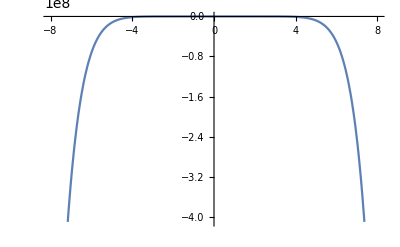

```mathematica
Plot[%97,{x,-8,8}]
```

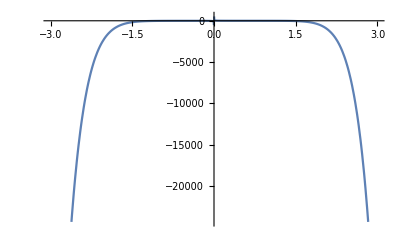

```mathematica
Plot[%97,{x,-3,3}]
```

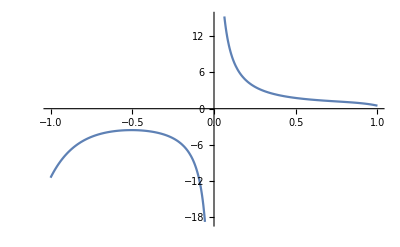

```mathematica
Plot[%97,{x,-1,1}]
```

```mathematica
Series[√x,{x,0,10}]
```

√x+O[x]^(21/2)

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
Manipulate[
Plot[x-x^3/6+x^5/120-10α x^7/5040+x^9/362880,{x,-5,5}]
,{α,-5,5}]
```

```mathematica
Manipulate[
Plot[x-x^3/6+x^5/120-10α x^7/5040+x^9/362880,{x,-5,5},PlotRange->{-10,10}]
,{α,-5,5}]
```

```mathematica
Manipulate[
Plot[
{Sin[x],x-x^3/6+x^5/120-10α x^7/5040+x^9/362880}
,{x,-5,5},PlotRange->{-10,10}]
,{α,-5,5}]
```

```mathematica
Manipulate[
Plot[
{Sin[x],x-x^3/6+x^5/120-10α x^7/5040+x^9/362880}
,{x,-5,5},PlotRange->{-10,10}]
,{{α,1},-5,5}]
```

```mathematica
FullSimplify[Normalize@{x,Sin[x]}.Normalize@{x,x-x^3/6+x^5/120-10α x^7/5040+x^9/362880},{x,α}∈Reals]
```

(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2)))

```mathematica
Manipulate[Plot[(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))),{x,-8,8}],{α,-8,8}]
```

```mathematica
Plot3D[
(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2)))
,{x,-8,8},{α,-8,8}]
```

-Graphics3D-

```mathematica
D[(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))),α]
```

(x^8 (x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504) (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]) (x^2+Sin[x]^2))/(182891520 ((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))^(3/2))-(x^7 Sin[x])/(504 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2)))

```mathematica
Solve[(x^8 (x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504) (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]) (x^2+Sin[x]^2))/(182891520 ((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))^(3/2))-(x^7 Sin[x])/(504 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2)))==0,α,Reals]
```

$Aborted

```mathematica
Integrate[(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))),{x,-5,5}]
```

$Aborted

```mathematica
Manipulate[Plot[(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))),{x,-8,8}],{α,-8,8}]
```

```mathematica
Manipulate[Plot[(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))),{x,-8,8}],{α,0,1}]
```

```mathematica
Manipulate[Plot[(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))),{x,-8,8},PlotRange->Full],{α,0,1}]
```

```mathematica
Manipulate[Plot[(x (362880 x+(362880-60480 x^2+3024 x^4+x^8-720 x^6 α) Sin[x]))/(362880 √((x^2+(x-x^3/6+x^5/120+x^9/362880-(x^7 α)/504)^2) (x^2+Sin[x]^2))),{x,-8,8},PlotRange->Full],{α,.9,.15}]
```

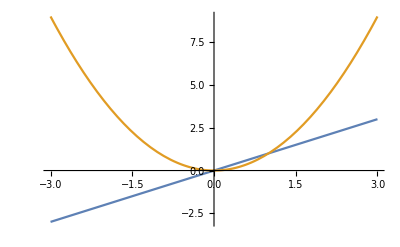

```mathematica
Plot[{x,x x},{x,-3,3}]
```

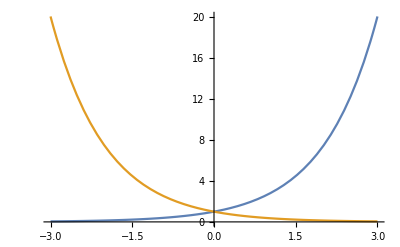

```mathematica
Plot[{Exp[x],Exp[-x]},{x,-3,3}]
```

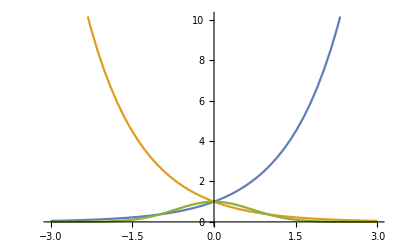

```mathematica
Plot[{Exp[x],Exp[-x],Exp[-x^2]},{x,-3,3}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

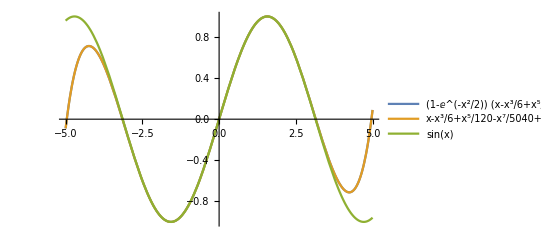

```mathematica
Plot[
{(1-ⅇ^(-x^2/2))(x-x^3/6+x^5/120-x^7/5040+x^9/362880)+(ⅇ^(-x^2/2))Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880,Sin[x]}
,{x,-5,5}
,PlotLegends->"Expressions"]
```

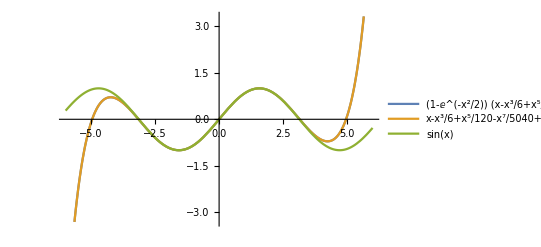

```mathematica
Plot[
{(1-ⅇ^(-x^2/2))(x-x^3/6+x^5/120-x^7/5040+x^9/362880)+(ⅇ^(-x^2/2))Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880,Sin[x]}
,{x,-6,6}
,PlotLegends->"Expressions"]
```

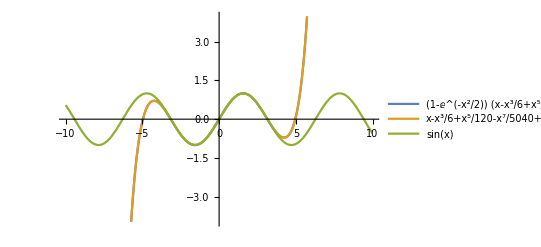

```mathematica
Plot[
{(1-ⅇ^(-x^2/2))(x-x^3/6+x^5/120-x^7/5040+x^9/362880)+(ⅇ^(-x^2/2))Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880,Sin[x]}
,{x,-10,10}
,PlotLegends->"Expressions"]
```

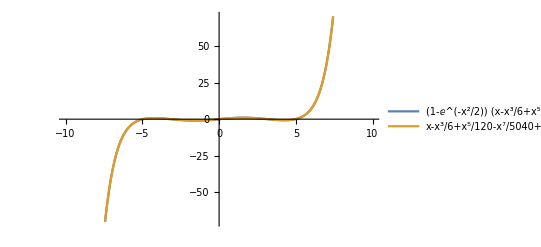

```mathematica
Plot[
{(1-ⅇ^(-x^2/2))(x-x^3/6+x^5/120-x^7/5040+x^9/362880)+(ⅇ^(-x^2/2))Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880}
,{x,-10,10}
,PlotLegends->"Expressions"]
```

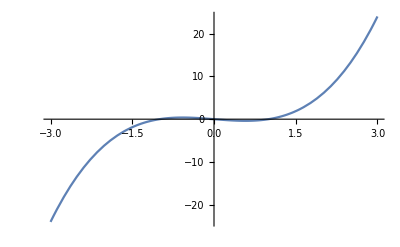

```mathematica
Plot[x^3-x,{x,-3,3}]
```

```mathematica
Plot[x^3-x,{x,-2,2}]
```

-Graphics-

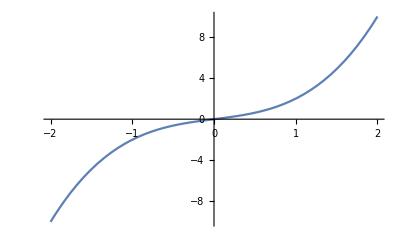

```mathematica
Plot[x^3+x,{x,-2,2}]
```

```mathematica
y''[x]/((√(1+y'[x]^2))^3)
```

y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
Map[Function[y,#]&,{x,x^3}]
```

{Function[y,x],Function[y,x^3]}

```mathematica
Map[Function[y,y''[x]/((1+y'[x]^2)^(3/2))]&,{Function[x,x],Function[x,x^3]}]
```

{Function[y,y''[x]/((1+y'[x]^2)^(3/2))],Function[y,y''[x]/((1+y'[x]^2)^(3/2))]}

```mathematica
Map[Function[y,(#''[x])/((1+(#'[x])^2)^(3/2))]&,{Function[x,x],Function[x,x^3]}]
```

{Function[y,(Function[x,x]''[x])/((1+(Function[x,x]'[x])^2)^(3/2))],Function[y,(Function[x,x^3]''[x])/((1+(Function[x,x^3]'[x])^2)^(3/2))]}

```mathematica
Map[(#''[x])/((1+(#'[x])^2)^(3/2))&,{Function[x,x],Function[x,x^3]}]
```

{0,(6 x)/((1+9 x^4)^(3/2))}

```mathematica
Table[x^i,{i,1,3}]
```

{x,x^2,x^3}

```mathematica
Map[Function[y,#]&,{x,x^2,x^3}]
```

{Function[y,x],Function[y,x^2],Function[y,x^3]}

```mathematica
Map[(#''[x])/((1+(#'[x])^2)^(3/2))&,{Function[x,x],Function[x,x^2],Function[x,x^3]}]
```

{0,2/((1+4 x^2)^(3/2)),(6 x)/((1+9 x^4)^(3/2))}

```mathematica
{0,2/((1+4 x^2)^(3/2)),(6 x)/((1+9 x^4)^(3/2))}/(Total@{0,2/((1+4 x^2)^(3/2)),(6 x)/((1+9 x^4)^(3/2))})
```

{0,2/((1+4 x^2)^(3/2) (2/((1+4 x^2)^(3/2))+(6 x)/((1+9 x^4)^(3/2)))),(6 x)/((1+9 x^4)^(3/2) (2/((1+4 x^2)^(3/2))+(6 x)/((1+9 x^4)^(3/2))))}

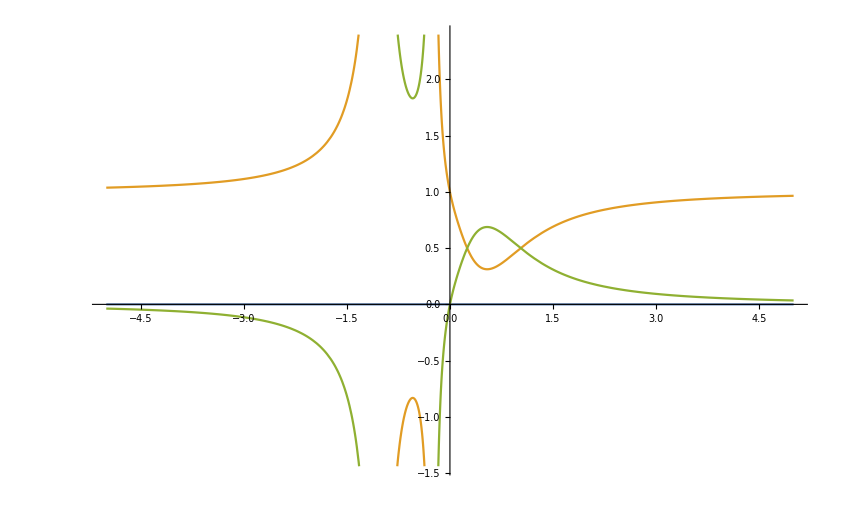

```mathematica
Plot[{0,2/((1+4 x^2)^(3/2) (2/((1+4 x^2)^(3/2))+(6 x)/((1+9 x^4)^(3/2)))),(6 x)/((1+9 x^4)^(3/2) (2/((1+4 x^2)^(3/2))+(6 x)/((1+9 x^4)^(3/2))))},{x,-5,5}]
```

```mathematica
Abs@{0,2/((1+4 x^2)^(3/2)),(6 x)/((1+9 x^4)^(3/2))}
```

{0,2/(Abs[1+4 x^2]^(3/2)),6 Abs[x/((1+9 x^4)^(3/2))]}

```mathematica
FullSimplify[{0,2/(Abs[1+4 x^2]^(3/2)),6 Abs[x/((1+9 x^4)^(3/2))]}/(Total@{0,2/(Abs[1+4 x^2]^(3/2)),6 Abs[x/((1+9 x^4)^(3/2))]}),x∈Reals]
```

{0,1/(1+3 ((1+4 x^2)/(1+9 x^4))^(3/2) Abs[x]),(3 (1+4 x^2)^(3/2) Abs[x])/((1+9 x^4)^(3/2)+3 (1+4 x^2)^(3/2) Abs[x])}

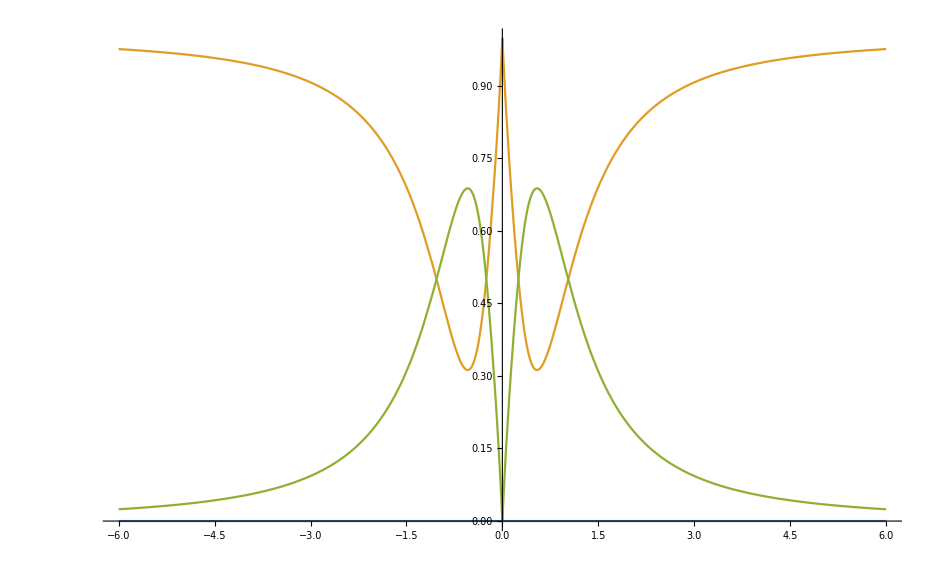

```mathematica
Plot[
{0,1/(1+3 ((1+4 x^2)/(1+9 x^4))^(3/2) Abs[x]),(3 (1+4 x^2)^(3/2) Abs[x])/((1+9 x^4)^(3/2)+3 (1+4 x^2)^(3/2) Abs[x])}
,{x,-6,6}]
```

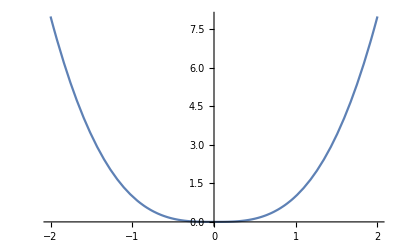

```mathematica
Plot[Abs[x^3],{x,-2,2}]
```

```mathematica
Table[Abs[x^i],{x,1,10}]
```

{1,2^Re[i],3^Re[i],4^Re[i],5^Re[i],6^Re[i],7^Re[i],8^Re[i],9^Re[i],10^Re[i]}

```mathematica
Table[Abs[x^i],{i,1,10}]
```

{Abs[x],Abs[x]^2,Abs[x]^3,Abs[x]^4,Abs[x]^5,Abs[x]^6,Abs[x]^7,Abs[x]^8,Abs[x]^9,Abs[x]^10}

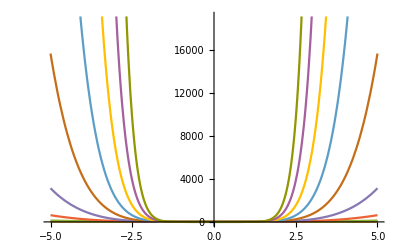

```mathematica
Plot[
{Abs[x],Abs[x]^2,Abs[x]^3,Abs[x]^4,Abs[x]^5,Abs[x]^6,Abs[x]^7,Abs[x]^8,Abs[x]^9,Abs[x]^10}
,{x,-5,5}]
```

```mathematica
FullSimplify[Normalize@{0,f''[x]}.Normalize@{1,f'[x]},x∈Reals]
```

(f'[x] f''[x])/(√(1+Abs[f'[x]]^2) Abs[f''[x]])

```mathematica
FullSimplify[Normalize@{0,f''[x]}.Normalize@{1,f'[x]},{x,f[x],f'[x],f''[x]}∈Reals]
```

(Sign[f''[x]] f'[x])/(√(1+f'[x]^2))

```mathematica
With[{f=Function[x,x^3]},
(Sign[f''[x]] f'[x])/(√(1+f'[x]^2))
]
```

(3 x^2 Sign[x])/(√(1+9 x^4))

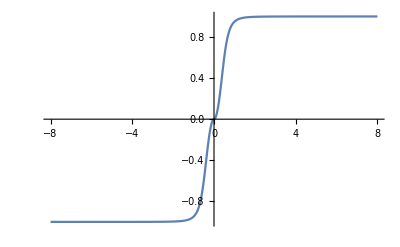

```mathematica
Plot[(3 x^2 Sign[x])/(√(1+9 x^4)),{x,-8,8}]
```

```mathematica
With[{f=Function[x,x^2]},
(Sign[f''[x]] f'[x])/(√(1+f'[x]^2))
]
```

(2 x)/(√(1+4 x^2))

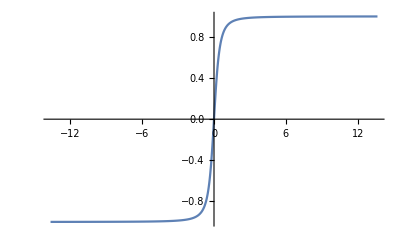

```mathematica
Plot[(2 x)/(√(1+4 x^2)),{x,-13.649999999999999,13.649999999999999}]
```

```mathematica
D[(2 x)/(√(1+4 x^2)),x]
```

-(8 x^2)/((1+4 x^2)^(3/2))+2/(√(1+4 x^2))

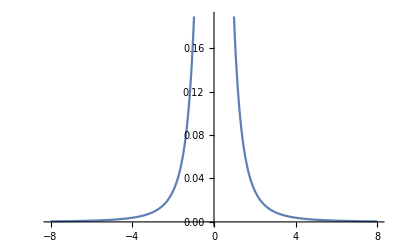

```mathematica
Plot[-(8 x^2)/((1+4 x^2)^(3/2))+2/(√(1+4 x^2)),{x,-8,8}]
```

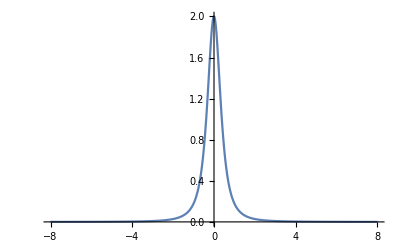

```mathematica
Plot[-(8 x^2)/((1+4 x^2)^(3/2))+2/(√(1+4 x^2)),{x,-8,8},PlotRange->Full]
```

```mathematica
D[(3 x^2 Sign[x])/(√(1+9 x^4)),x]
```

-(54 x^5 Sign[x])/((1+9 x^4)^(3/2))+(6 x Sign[x])/(√(1+9 x^4))+(3 x^2 Sign'[x])/(√(1+9 x^4))

```mathematica
FullSimplify[-(54 x^5 Sign[x])/((1+9 x^4)^(3/2))+(6 x Sign[x])/(√(1+9 x^4))+(3 x^2 Sign'[x])/(√(1+9 x^4))]
```

(3 x (2 Sign[x]+x (1+9 x^4) Sign'[x]))/((1+9 x^4)^(3/2))

```mathematica
Plot[(3 x (2 Sign[x]+x (1+9 x^4) Sign'[x]))/((1+9 x^4)^(3/2)),{x,-2,2}]
```

-Graphics-

```mathematica
Sign[x]
```

Sign[x]

```mathematica
D[Sign[x], x]
```

Sign'[x]

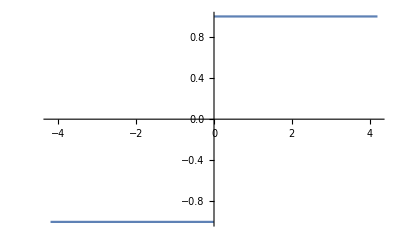

```mathematica
Plot[Sign[x],{x,-4.2,4.2}]
```

```mathematica
Plot[Sign'[x],{x,-2,2}]
```

-Graphics-

```mathematica
(3 x (2 Sign[x]))/((1+9 x^4)^(3/2))
```

(6 x Sign[x])/((1+9 x^4)^(3/2))

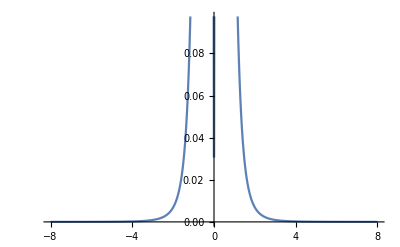

```mathematica
Plot[(6 x Sign[x])/((1+9 x^4)^(3/2)),{x,-8,8}]
```

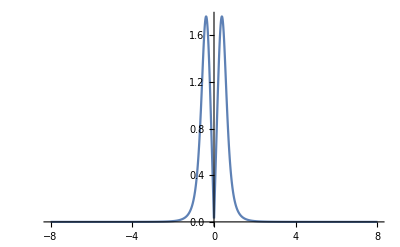

```mathematica
Plot[(6 x Sign[x])/((1+9 x^4)^(3/2)),{x,-8,8},PlotRange->Full]
```

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
With[{f=Function[x,x-x^3/6+x^5/120-x^7/5040+x^9/362880]},
(Sign[f''[x]] f'[x])/(√(1+f'[x]^2))
]
```

((1-x^2/2+x^4/24-x^6/720+x^8/40320) Sign[-x+x^3/6-x^5/120+x^7/5040])/(√(1+(1-x^2/2+x^4/24-x^6/720+x^8/40320)^2))

```mathematica
FullSimplify[((1-x^2/2+x^4/24-x^6/720+x^8/40320) Sign[-x+x^3/6-x^5/120+x^7/5040])/(√(1+(1-x^2/2+x^4/24-x^6/720+x^8/40320)^2))]
```

((1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320) Sign[x] Sign[-5040+840 x^2-42 x^4+x^6])/(√(1+(1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320)^2))

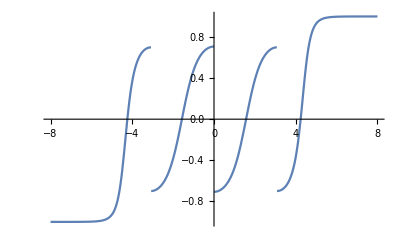

```mathematica
Plot[((1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320) Sign[x] Sign[-5040+840 x^2-42 x^4+x^6])/(√(1+(1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320)^2)),{x,-8,8}]
```

```mathematica
FullSimplify[((1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320) Sign[x] Sign[-5040+840 x^2-42 x^4+x^6])/(√(1+(1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320)^2)),x∈Reals]
```

((1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320) Sign[x] Sign[-5040+840 x^2-42 x^4+x^6])/(√(1+(1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320)^2))

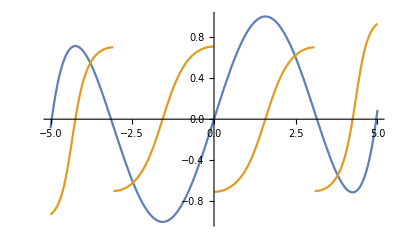

```mathematica
Plot[
{x-x^3/6+x^5/120-x^7/5040+x^9/362880,((1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320) Sign[x] Sign[-5040+840 x^2-42 x^4+x^6])/(√(1+(1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320)^2))}
,{x,-5,5},PlotRange->Full]
```

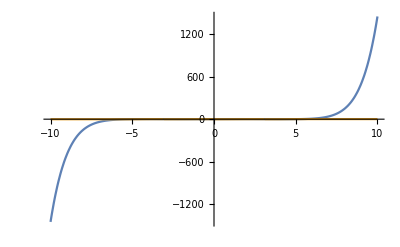

```mathematica
Plot[
{x-x^3/6+x^5/120-x^7/5040+x^9/362880,((1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320) Sign[x] Sign[-5040+840 x^2-42 x^4+x^6])/(√(1+(1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320)^2))}
,{x,-10,10},PlotRange->Full]
```

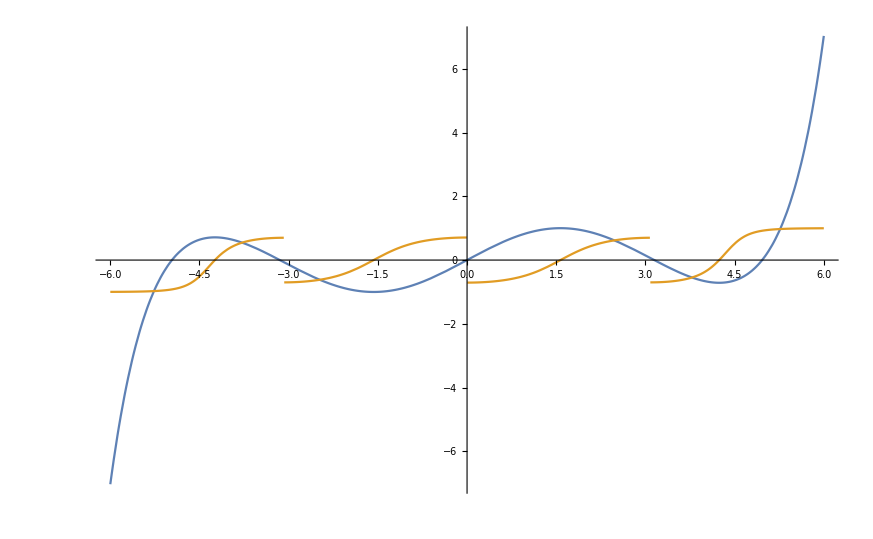

```mathematica
Plot[
{x-x^3/6+x^5/120-x^7/5040+x^9/362880,((1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320) Sign[x] Sign[-5040+840 x^2-42 x^4+x^6])/(√(1+(1+(x^2 (-20160+1680 x^2-56 x^4+x^6))/40320)^2))}
,{x,-6,6},PlotRange->Full]
```

```mathematica
With[{f=Sin},
(Sign[f''[x]] f'[x])/(√(1+f'[x]^2))
]
```

-(Cos[x] Sign[Sin[x]])/(√(1+Cos[x]^2))

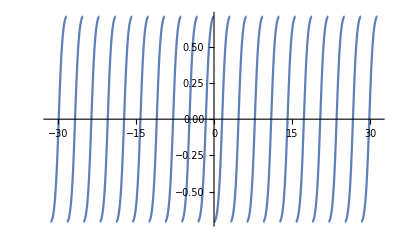

```mathematica
Plot[-(Cos[x] Sign[Sin[x]])/(√(1+Cos[x]^2)),{x,-10 π,10 π}]
```

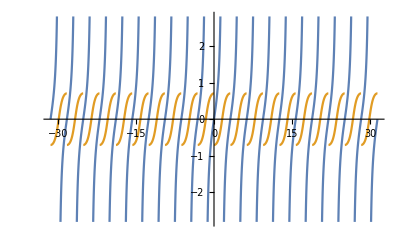

```mathematica
Plot[{Tan[x],-(Cos[x] Sign[Sin[x]])/(√(1+Cos[x]^2))},{x,-10 π,10 π}]
```

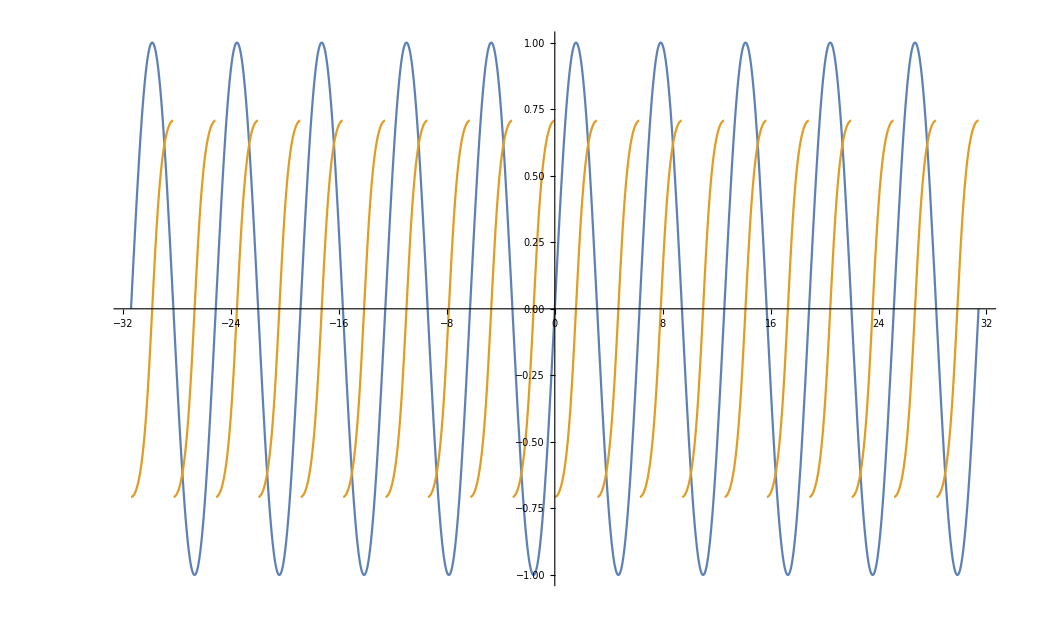

```mathematica
Plot[{Sin[x],-(Cos[x] Sign[Sin[x]])/(√(1+Cos[x]^2))},{x,-10 π,10 π}]
```

```mathematica
D[-(Cos[x] Sign[Sin[x]])/(√(1+Cos[x]^2)),x]
```

-(Cos[x]^2 Sign[Sin[x]] Sin[x])/((1+Cos[x]^2)^(3/2))+(Sign[Sin[x]] Sin[x])/(√(1+Cos[x]^2))-(Cos[x]^2 Sign'[Sin[x]])/(√(1+Cos[x]^2))

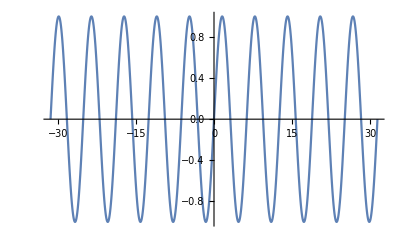

```mathematica
Plot[{Sin[x],-(Cos[x]^2 Sign[Sin[x]] Sin[x])/((1+Cos[x]^2)^(3/2))+(Sign[Sin[x]] Sin[x])/(√(1+Cos[x]^2))-(Cos[x]^2 Sign'[Sin[x]])/(√(1+Cos[x]^2))},{x,-10 π,10 π}]
```

```mathematica
-(Cos[x]^2 Sign[Sin[x]] Sin[x])/((1+Cos[x]^2)^(3/2))+(Sign[Sin[x]] Sin[x])/(√(1+Cos[x]^2))
```

-(Cos[x]^2 Sign[Sin[x]] Sin[x])/((1+Cos[x]^2)^(3/2))+(Sign[Sin[x]] Sin[x])/(√(1+Cos[x]^2))

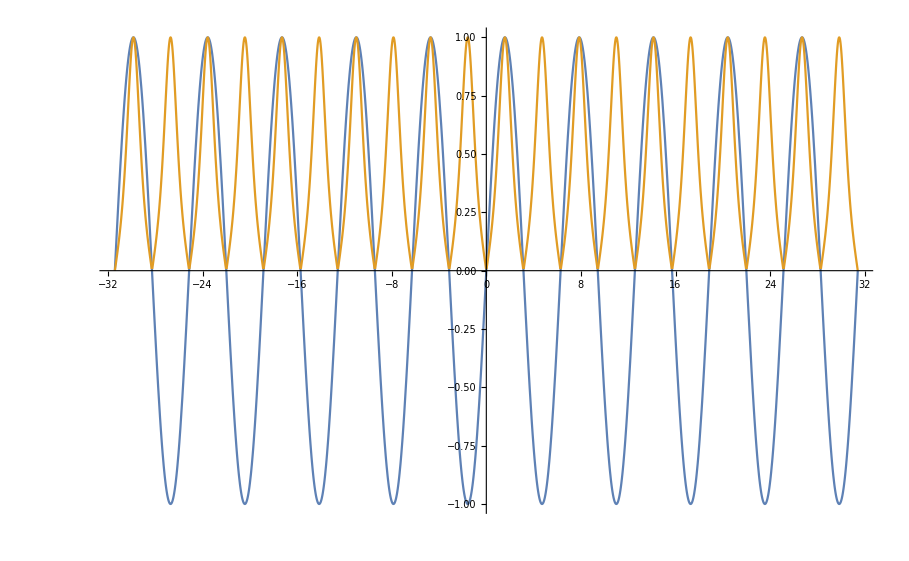

```mathematica
Plot[{Sin[x],-(Cos[x]^2 Sign[Sin[x]] Sin[x])/((1+Cos[x]^2)^(3/2))+(Sign[Sin[x]] Sin[x])/(√(1+Cos[x]^2))},{x,-10 π,10 π}]
```

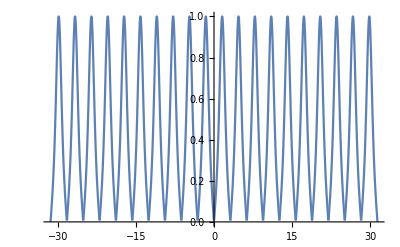

```mathematica
Plot[-(Cos[x]^2 Sign[Sin[x]] Sin[x])/((1+Cos[x]^2)^(3/2))+(Sign[Sin[x]] Sin[x])/(√(1+Cos[x]^2)),{x,-10 π,10 π}]
```

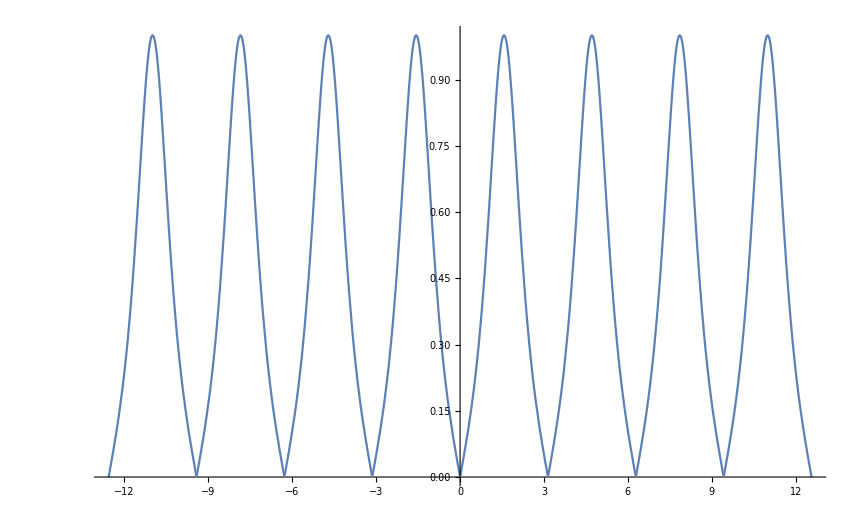

```mathematica
Plot[-(Cos[x]^2 Sign[Sin[x]] Sin[x])/((1+Cos[x]^2)^(3/2))+(Sign[Sin[x]] Sin[x])/(√(1+Cos[x]^2)),{x,-4π,4 π}]
```

```mathematica
D[f[x],x]==λ f[x]
```

f'[x]==λ f[x]

```mathematica
DSolve[f'[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x λ) C[1]}}

```mathematica
{{f[x]->ⅇ^(x λ) C[1]}}⟦1,1,2⟧
```

ⅇ^(x λ) C[1]

```mathematica
Exp[D[f[x],x]/f[x]]==λ f[x]
```

ⅇ^(f'[x]/f[x])==λ f[x]

```mathematica
DSolve[ⅇ^(f'[x]/f[x])==λ f[x],{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→(ⅇ^(ⅇ^(x+C[1])))/λ}}

```mathematica
Exp[D[f[x],x]/f[x]]==x
```

ⅇ^(f'[x]/f[x])==x

```mathematica
DSolve[ⅇ^(f'[x]/f[x])==x,{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→ⅇ^(-x+x Log[x]) C[1]}}

```mathematica
Exp[D[f[x],x]/f[x]]==f[x]
```

ⅇ^(f'[x]/f[x])==f[x]

```mathematica
DSolve[ⅇ^(f'[x]/f[x])==f[x],{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→ⅇ^(ⅇ^(x+C[1]))}}

```mathematica
Exp[D[ⅇ^(-x+x Log[x]),x]/ⅇ^(-x+x Log[x])]
```

x

```mathematica
y''[x]/((√(1+y'[x]^2))^3)==x
```

y''[x]/((1+y'[x]^2)^(3/2))==x

```mathematica
DSolve[y''[x]/((1+y'[x]^2)^(3/2))==x,{y[x],y[x]},{x}]
```

{{y[x]→C[2]-(√((-2+x^2+2 C[1])/(-1+C[1])) √((2+x^2+2 C[1])/(1+C[1])) ((-1+C[1]) EllipticE[ⅈ ArcSinh[x √(1/(2+2 C[1]))],(1+C[1])/(-1+C[1])]+EllipticF[ⅈ ArcSinh[x √(1/(2+2 C[1]))],(1+C[1])/(-1+C[1])]))/(√(1/(2+2 C[1])) √(-4+x^4+4 x^2 C[1]+4 C[1]^2))},{y[x]→C[2]+(√((-2+x^2+2 C[1])/(-1+C[1])) √((2+x^2+2 C[1])/(1+C[1])) ((-1+C[1]) EllipticE[ⅈ ArcSinh[x √(1/(2+2 C[1]))],(1+C[1])/(-1+C[1])]+EllipticF[ⅈ ArcSinh[x √(1/(2+2 C[1]))],(1+C[1])/(-1+C[1])]))/(√(1/(2+2 C[1])) √(-4+x^4+4 x^2 C[1]+4 C[1]^2))}}

```mathematica
(√((-2+x^2+2 C[1])/(-1+C[1])) √((2+x^2+2 C[1])/(1+C[1])) ((-1+C[1]) EllipticE[ⅈ ArcSinh[x √(1/(2+2 C[1]))],(1+C[1])/(-1+C[1])]+EllipticF[ⅈ ArcSinh[x √(1/(2+2 C[1]))],(1+C[1])/(-1+C[1])]))/(√(1/(2+2 C[1])) √(-4+x^4+4 x^2 C[1]+4 C[1]^2))/.C[1]->0
```

(√2 √(2-x^2) √(2+x^2) (-EllipticE[ⅈ ArcSinh[x/(√2)],-1]+EllipticF[ⅈ ArcSinh[x/(√2)],-1]))/(√(-4+x^4))

```mathematica
Plot[x,{x,-2,2}]
```

-Graphics-

```mathematica
ComplexPlot[(√2 √(2-x^2) √(2+x^2) (-EllipticE[ⅈ ArcSinh[x/(√2)],-1]+EllipticF[ⅈ ArcSinh[x/(√2)],-1]))/(√(-4+x^4)),{x,-5-5I,5+5I}]
```

-Graphics-